# Example Environment - Factors of an integer

I would recommend to evaluate the whole notebook

```mathematica
(*Import Directly from GitHub - Can alternativly download and import from mathematica's applcations folder*)
Get["https://raw.githubusercontent.com/Airsofter4692/GAMathematica/main/Genetic.m"];
```

Genetic: Genetic Evolution of Bit Sequences

S. A. Abel, A. Constantin, T. R. Harvey and A. Lukas

Last Update: 9 June 2022

Execute rr for help. Current Genetic options:

{InitModule→MonadEnv`MonadBitInit,FitnessModule→MonadEnv`MonadFitness,GenSize→50,MutationRate→0.01,KeepFitest→False,NumCuts→1,SelectionMethod→Roulette,Alpha→3}

Note, as it says above, run the command “?Genetic” to get information on functions and options

```mathematica
?Genetic
```

```mathematica
?GeneticModules
```

```mathematica
?GeneticOptions
```

## Environment - Example Environment for Finding Factors of an Integer

```mathematica
(*Example Parameter values - Will be set again later *)
numberOfBits=10;
intToFactor=1000;

(*Define a fitness function - The aim is the maximise the fitness*)
Options[FitnessFunction]:={"OutFormat"->"short"};
FitnessFunction[bitlst_,opt___]:=Module[{state,fitness,n,m,terminal},
n=intToFactor;
m=FromDigits[bitlst,2]+1;
fitness=-(Mod[n,m]/m);
If[fitness==0,terminal=True,terminal=False];
state=Association[{"Integers"->{n,m},"Bits"->bitlst,"Fitness"->fitness,"Terminal"->terminal}];
state];

(*Define an initialisation function - This will be used to generate the population in generation 0*)
IntegerInit[opt___]:=Module[{numbits,bitlst},
numbits=numberOfBits;
bitlst=Table[RandomInteger[{0,1}],{numbits}];
FitnessFunction[bitlst,numbits]
];
```

```mathematica
(*Set the options for the genetic package, so that they use these example functions*)
SetOptions[Genetic,{"InitModule"->IntegerInit,"FitnessModule"->FitnessFunction,"GenSize"->100,"SelectionMethod"->"Ranking","MutationRate"->0.004,"Alpha"->4,"KeepFitest"->True}];
```

## Example Run - Run This Last

```mathematica
(*Set Paramters for Environment - GA will return factors of intToFactor*)
intToFactor=97008;
numberOfBits=Floor[N[Log[2,intToFactor]]];
```

```mathematica
(*Run GA with random initial*)
pop=EvolvePopulation[{},100];
Select[Union[Flatten[pop]],("Fitness"/.#)==0&]
```

{<|Integers→{97008,12126},Bits→{0,0,1,0,1,1,1,1,0,1,0,1,1,1,0,1},Fitness→0,Terminal→True|>}

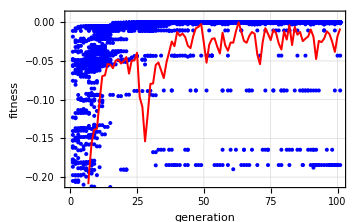
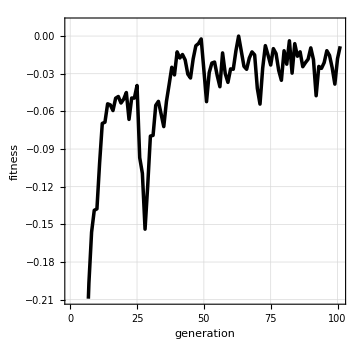
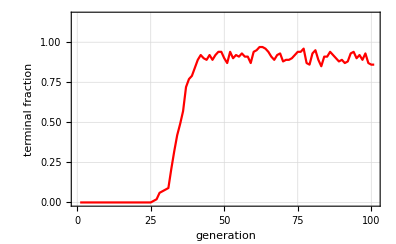
{-Graphics3D-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{PlotFitness[pop,"Method"->"Histogram"],
PlotFitness[pop,"Method"->"Points"],
PlotFitness[pop,"Method"->"Contours"],
PlotTerminal[pop]}
```